## Bayesian Statistics, Assignment for Tuesday, Nov. 5

## Reading

Recall that we are skipping Chapter 7 completely because there isn’t enough new stuff in it to make it worth spending half a week on. Jump back in at the last half of Chapter 8, pp. 95-107. (If you were also to try to read the first half of Chapter 8, pp. 88-94, I think you will find it to be a mind-numbing review of what we covered in Young.)

After finishing the last half of Chapter 8, continue in Chapter 9, pp. 108-122 (this is yet more review of Young but in this case the review is more advanced and useful). Stop at the end of p. 122. This is where Donovan and Mickey start bringing Bayes’ Theorem back in, but this time for probability distributions like the Gaussian distribution. We’ll save the rest of Chapter 9 for the next reading.

## Review/Overview

On the last day before break, to give you an idea where we would be heading soon, I derived the following version of Bayes theorem, appropriate when the theory involves a continuous parameter, a, and I also wrote up the derivation in a handout called “A Continuum of Hypotheses.”

P(a^*|data)Δ a^*=(P(data|a^*)P(a^*)Δ a^*)/(∫_a_min^a_max P(data|a)P(a)da)

This is also Eq. 9.31 in Donovan and Mickey Chapter 9, bottom of p. 122, except my notation is slightly more precise and intuitive (IMHO ;) ), and I called the theoretical parameter a, whereas Donovan and Mickey called it θ.

There is no need to go back and study the derivation any more at the moment. Instead, let’s gain familiarity with it by applying it to something interesting!

## For Problem Set 11 — The Mug Breakage Problem

### Description of the Prior and the Data

Imagine that after a careful study of the previous year’s mug purchase records, you have come to the conclusion that the BH team on average breaks 2 to 6 mugs per week. Within this range, you have no further information as to any part of the range being more favored than another. Therefore, the prior, P(a) looks like this:

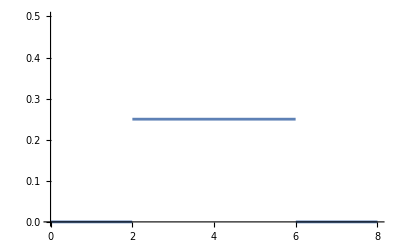

```mathematica
prior[a_]:=If[2<=a<=6, 1/(6-2),0];
Plot[prior[a],{a, 0, 8}, PlotRange->{{0, 8},{0,0.5}}]
```

To refine this range of a values, you decide to take weekly data for three weeks. You find that in the first week, 1 mug was broken, in the second week 6 mugs were broken, and in the third week, 4 mugs were broken.

### Step 1 — Computing the Likelihood Function

Act as if a were known. (Remember the likelihood is P(data|a). That means we are pretending that a is given.

(a) Write down the probability of having 1 mug broken in the first week. You may have to remind yourself the formula for the Poisson distribution. It was on p. 59 of Young. You are just being asked to plug n=1 into this formula.

(b) Repeat, but with n=6 for the second week.

(c) Repeat, but with n=4 for the third week.

(d) Take the product of what you got in (a), (b), and (c). This is the likelihood of getting this data.

### Step 2 — Tabulate the Likelihood

```mathematica
poisson[n_, a_]:=a^n/Factorial[n] Exp[-a];
```

```mathematica
likelihood[{n1_, n2_, n3_}, a_]:=poisson[n1, a]*poisson[n2, a]*poisson[n3, a];
TableForm[Table[{a,If[4<=a<=6, "", likelihood[{1, 6, 4}, a]]}, {a, 0, 8, 0.5}], TableHeadings->{None, {"a", "P(data|a)"}}]
```

a | P(data|a)
0. | 0.
0.5 | 6.30499×10^-9
1. | 2.8812×10^-6
1.5 | 0.0000556077
2. | 0.000293778
2.5 | 0.000763111
3. | 0.00126514
3.5 | 0.00153855
4. | 
4.5 | 
5. | 
5.5 | 
6. | 
6.5 | 0.000172092
7. | 0.0000867662
7.5 | 0.0000413527
8. | 0.0000187663

To make your life easier, I had Mathematica compute and display all but five of the values that you will need to make a good graph.

### Step 3 — Graph the Likelihood

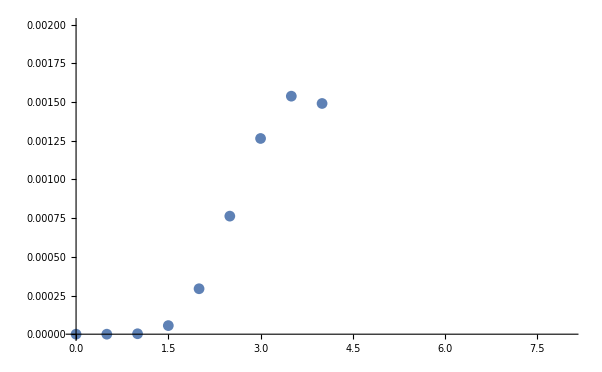

```mathematica
ListPlot[Table[{a, likelihood[{1, 6, 4}, a]}, {a, 0, 4, 0.5}], PlotRange->{{0, 8},{0,0.002}}]
```

Again, to make your life easier, I had Mathematica compute and plot half the points. I am trying to make sure you know how to create and plot the points without burying you in long calculator sessions.

Once you have all the points plotted, freehand a nice smooth curve through them.

### Step 4 — Tabulate the Product of the Likelihood and the Prior

In Step 2, you tabulated the likelihood. Take a look at the graph of the prior. It is 0 unless a is between 2 and 6. If a is between 2 and 6, it is 1/4. Using these facts, you should be able to quickly tabulate the product of the likelihood and the prior.

```mathematica
TableForm[Table[{a,"            "}, {a, 0, 8, 0.5}], TableHeadings->{None, {"a", "P(data|a)*P(a)"}}]
```

a | P(data|a)*P(a)
0. |             
0.5 |             
1. |             
1.5 |             
2. |             
2.5 |             
3. |             
3.5 |             
4. |             
4.5 |             
5. |             
5.5 |             
6. |             
6.5 |             
7. |             
7.5 |             
8. |

### Step 5 — Graph the Product of the Likelihood and the Prior

In Step 4, you tabulated the product of the likelihood and the prior. Now you are going to graph it.

```mathematica
product[a_]:=likelihood[{1,6,4},a]*prior[a]
Plot[{},{a,0,8}, PlotRange->{{0, 8},{0,0.0004}}]
```

-Graphics-

### Remaining Steps

There are still two a few more steps to go!! Remember that we are trying to compute

P(a^*|data)Δ a^*=(P(data|a^*)P(a^*)Δ a^*)/(∫_a_min^a_max P(data|a)P(a)da)

Step 6 is to do the integral in the denominator, 
Step 7 is to make a table of the posterior, which is P(data|a^*)P(a^*) divided by the denominator from Step 6.
Step 8 is to plot the posterior.
Step 9 is to interpret the posterior.

HOWEVER! We have to leave something for our presenters to do, so you can stop at Step 5.